Kaushik Chakram 
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     phys 425 &01
                                                                                                                    March 06,2018

Problem 2.27)b)

```mathematica
$Assumptions = {x,t,A,a,k,m,ℏ,α,Subscript[α, 1],Subscript[V, 0],Subscript[a, 1],n} ∈ Reals
```

(x|t|A|k|n)∈Reals

```mathematica
α:=ℏ^2/(m*a^2)
P1 :=(m*a* α)/ℏ^2*(1+ⅇ^(-2*η))
Subscript[α, 1]:=α/4
```

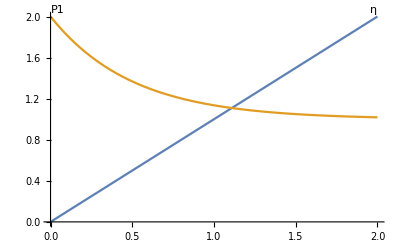

```mathematica
a:=1
m:=1
ℏ:=1
Plot[{η,P1},{η,0,2},PlotLabels-> Placed[{"η","P1"},Above]]
```

```mathematica
N[Solve[η==P1,η],8]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→1.1088576}}

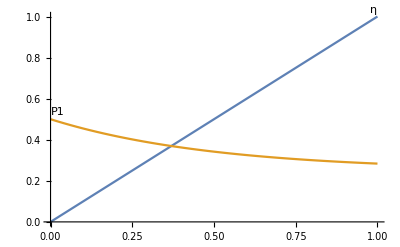

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→0.36941752}}

```mathematica
P2 :=(m*a* Subscript[α, 1])/ℏ^2*(1+ⅇ^(-2*η))
Plot[{η,P2},{η,0,1},PlotLabels-> Placed[{"η","P1"},Above]]
N[Solve[η==P2],8] (* Now we must account for the odds solutions.*)
```

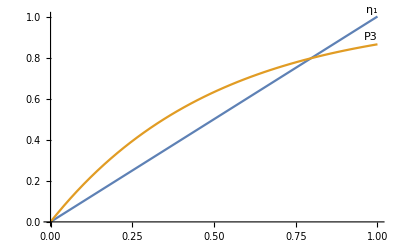

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η_1→0},{η_1→0.79681213}}

```mathematica
P3 :=(m*a* α)/ℏ^2*(1-(ⅇ^(-2*Subscript[η, 1])))
Plot[{Subscript[η, 1],P3},{Subscript[η, 1],0,1},PlotLabels-> Placed[{"η_1","P3"},Above]]
N[Solve[Subscript[η, 1]==P3],8](* The intersection at Subscript[η, 1]= 0 implies the energy is zero so we pick the other solution.*)
```

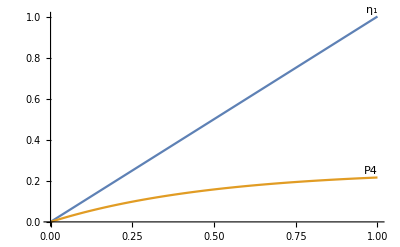

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η_1→0},{η_1→-0.6282156}}

```mathematica
P4 :=(m*a* Subscript[α, 1])/ℏ^2*(1-(ⅇ^(-2*Subscript[η, 1])))
Plot[{Subscript[η, 1],P4},{Subscript[η, 1],0,1},PlotLabels-> Placed[{"η_1","P4"},Above]]
N[Solve[Subscript[η, 1]==P4],8]
```

1)Problem 2.29)

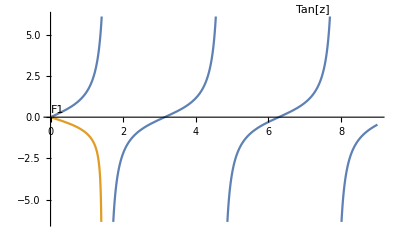

```mathematica
F1:= -1/(√(((√2)/z)^2-1))
Plot[{Tan[z],F1},{z,0,9},PlotLabels-> Placed[{"Tan[z]","F1"},Above]](*No bound state here.*)
```

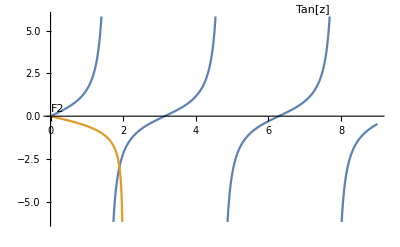

```mathematica
F2:= -1/(√((2/z)^2-1))
Plot[{Tan[z],F2},{z,0,9},PlotLabels-> Placed[{"Tan[z]","F2"},Above]]
(* One bound state here.*)
```

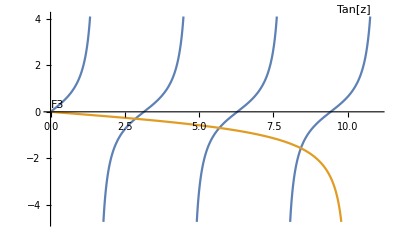

```mathematica
F3:= -1/(√((10/z)^2-1))
Plot[{Tan[z],F3},{z,0,11},PlotLabels-> Placed[{"Tan[z]","F3"},Above]]
(* Three bound states here.*)
```

```mathematica
Integrate[(1/(√Subscript[a, 1]))*(√(2/Subscript[a, 1]))Sin[(π*x)/Subscript[a, 1]]*(Sin[(n*π*x)/(2*Subscript[a, 1])]),{x,0,Subscript[a, 1]}]
```

(4 √2 Sin[(n π)/2])/(4 π-n^2 π)

```mathematica
C1[n_]:=((4 √2) *Sin[(n π)/2])/(4 π-n^2 π) (*Here we are setting it up to calculate the probabilities for the first 6 states*)
```

```mathematica
(C1[1])^2
```

32/(9 π^2)

```mathematica
(Integrate[(1/(√Subscript[a, 1]))*(√(2/Subscript[a, 1]))Sin[(π*x)/Subscript[a, 1]]*(Sin[(2*π*x)/(2*Subscript[a, 1])]),{x,0,Subscript[a, 1]}])^2
```

1/2

```mathematica
(C1[3])^2
```

32/(25 π^2)

```mathematica
(C1[4])^2
```

0

```mathematica
(C1[5])^2
```

32/(441 π^2)

```mathematica
(C1[6])^2
```

0

```mathematica
Integrate[(-ℏ^2/(2*m))*(√(2/Subscript[a, 1]))^2 Sin[(π*x)/Subscript[a, 1]]*D[(Sin[(π*x)/Subscript[a, 1]]),{x,2}],{x,0,Subscript[a, 1]}] (* This is just Subscript[E, 2]*)
```

(π^2 ℏ^2)/(2 m a_1^2)